### Code was tested with Mathematica 11.0 Written by Bob Lansdorp, PhD bob.lansdorp@gmail.com

# Diffusion Equations with Different Boundary Conditions

```mathematica
ClearAll["Global`*"] (* First reset all the variables to clean up workspace *)
```

## Neumann Boundary Condition Analytic Solution

```mathematica
InfinityApproximation = 50; (* used for truncating infinite series *)
(* Start by defining the equation in terms of c *)
(* eqFick=D[cBar[xbar,t],t]== Diff D[cBar[xBar,tBar],{x,2}];*) (* the diffusion equation *) 
(* xBar = x/L, αBar=α Diff/L , tBar = t D/L^2 *)
 eqFickCBar=D[cBar[xBar,tBar],tBar]==D[cBar[xBar,tBar],{xBar,2}]; (* the non-dimensionalized diffusion equation *) 
ic=cBar[xBar,0]== 0 ;
bc1 =cBar[0,tBar]==1 ;
bcNeumann = Derivative[1,0][cBar][1,tBar]==0;
```

```mathematica
solNeumannAnalytic=DSolveValue[{eqFickCBar,ic, bc1, bcNeumann},cBar[xBar,tBar],{xBar,tBar}, Assumptions->{xBar∈Reals,0<xBar<1, tBar>0}]
```

1+2 (2 ⅇ^(-1/4 π^2 tBar (-1+2 K[1])^2) Sin[1/2 π xBar (-1+2 K[1])])/(π-2 π K[1])K[1]1∞

```mathematica
solNeumannNumeric= Activate[solNeumannAnalytic/.{Infinity->InfinityApproximation}];
```

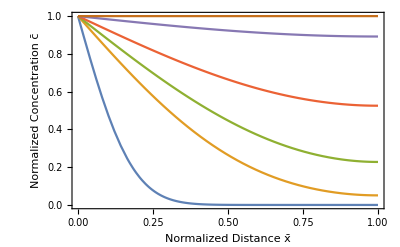

```mathematica
NeumannPlot = Plot[{solNeumannNumeric/.{tBar->0.01}, solNeumannNumeric/.{tBar->0.1},solNeumannNumeric/.{tBar->0.2},solNeumannNumeric/.{tBar->0.4},solNeumannNumeric/.{tBar->1},solNeumannNumeric/.{tBar->10}}, {xBar,0,1},PlotRange->{{0,1},{0,1}},Frame->True, FrameLabel->{"Normalized Distance x̄","Normalized Concentration c̄"}]
```

## Dirichlet Boundary Condition Analytic Solution

```mathematica
bcDirichlet =cBar[1,tBar] == 0;
```

```mathematica
solDirichletAnalytic=DSolveValue[{eqFickCBar,ic, bc1, bcDirichlet},cBar[xBar,tBar],{xBar,tBar}, Assumptions->{ 0<xBar<1, tBar>0}]
```

1-xBar-(2 (ⅇ^(-π^2 tBar K[1]^2) Sin[π xBar K[1]])/K[1]K[1]1∞)/π

```mathematica
(* Now obtain the Dirichlet solution *)
```

```mathematica
solDirichletNumeric = Activate[solDirichletAnalytic/.{Infinity->InfinityApproximation}];
```

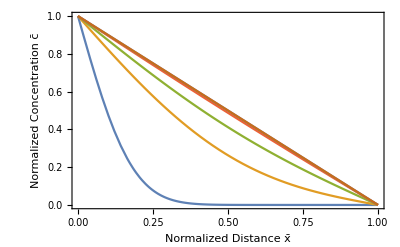

```mathematica
DirichletPlot = Plot[{solDirichletNumeric/.{tBar->0.01}, solDirichletNumeric/.{tBar->0.1},solDirichletNumeric/.{tBar->0.2},solDirichletNumeric/.{tBar->0.4},solDirichletNumeric/.{tBar->1},solDirichletNumeric/.{tBar->10}}, {xBar,0,1},PlotRange->{{0,1},{0,1}},Frame->True, FrameLabel->{"Normalized Distance x̄","Normalized Concentration c̄"}]
```

## Sensor response

```mathematica
sensorDirichlet = -D[solDirichletNumeric,xBar]/.{xBar->1};
```

```mathematica
sensorNeumann = solNeumannNumeric/.{xBar->1};
```

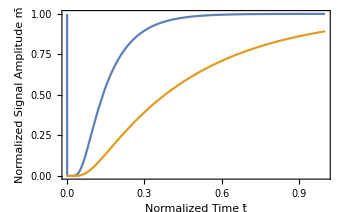

```mathematica
Plot[{sensorDirichlet, sensorNeumann}, {tBar,0,1}, PlotRange->{Automatic, {0,1}}, Frame->True, FrameLabel->{"Normalized Time t̄","Normalized Signal Amplitude m̄"}]
```

## Response time using the integrated sensor output ratio

```mathematica
integratedNeumann= Integrate[sensorNeumann,{tBar,0,τ}];
```

```mathematica
integratedDirichlet = Integrate[sensorDirichlet,{tBar,0,τ}];
```

```mathematica
Plot[{integratedNeumann, integratedDirichlet}, {τ,0,2}, PlotRange->{Automatic, Automatic}]; (* sanity check *)
```

```mathematica
(* if signal = m(t-tintercept).. then tintercept=-signal/m-t... and since m = 1, then tintercept = -signal+t
```

```mathematica
NeumanTIntercept = Limit[(-integratedNeumann+τ),τ->∞];
```

```mathematica
DirichletTIntercept = Limit[(-integratedDirichlet+τ),τ->∞];
```

```mathematica
N[NeumanTIntercept/DirichletTIntercept] (* the ratio of t intercepts - gives a number to how much faster a Flux based sensor is than a concentration sensor*)
```

3.00071

## Sanity checks : spatial domain only example solutions

```mathematica
(* First the Dirichlet *)
```

```mathematica
DSolve[{X''[x] +μ^2 X[x]==0, X[0] ==0, X[1]==0},X[x],x,Assumptions->{μ∈ Reals, μ>0 , 0<x<1}]
```

{{X[x]→Piecewise[{{C[1] Sin[x μ], n∈Integers&&0<x<1&&((n≥1&&μ==2 n π)||(n≥0&&μ==π+2 n π))}, {0, True}}]}}

```mathematica
(* Then the Neumann *)
```

```mathematica
DSolve[{X''[x] +μ^2X[x]==0, X[0] ==0, X'[1]==0},X[x],x,Assumptions->{μ∈ Reals, μ>0 , 0<x<1}]
```

{{X[x]→Piecewise[{{C[1] Sin[x μ], n∈Integers&&0<x<1&&((n≥1&&μ==1/2 (-π+4 n π))||(n≥0&&μ==1/2 (π+4 n π)))}, {0, True}}]}}

```mathematica
(* Then the Robin *)
```

```mathematica
DSolve[{X''[x] +μ^2X[x]==0, X[0] ==0, X'[1]==-α X[1]},X[x],x,Assumptions->{μ∈ Reals, μ>0 , 0<x<1, α>0}]
```

{{X[x]→Piecewise[{{C[1] Sin[x μ], n∈Integers&&α==-μ Cot[μ]&&0<x<1&&((n≥1&&1/2 (-π+4 n π)<μ<2 n π)||(n≥0&&1/2 (π+4 n π)<μ<π+2 n π))}, {0, True}}]}}

## Robin Boundary Condition

```mathematica
(* use the Daileda method to solve Robin boundary conditions *)
(* we will solve for α = 1, but any positive number is possible *)
α = 1;
fTest[xbar_]:=(1-α  (xbar)/(1+α )) (* the steady state solution *) 
(* first get the values of μN *)
```

```mathematica
μN[n_,L_, α_]:=μ/.FindRoot[Tan[μ L] == -μ/α ,{μ,((2n-1)π/(2 L)+n π/ L)/2,(2n-1)π/(2 L),n π/ L}]
```

```mathematica
μNTable = Table[μN[i,1,α],{i,1,InfinityApproximation}]
```

{2.02876,4.91318,7.97867,11.0855,14.2074,17.3364,20.4692,23.6043,26.7409,29.8786,33.017,36.156,39.2954,42.4351,45.575,48.7152,51.8556,54.9961,58.1367,61.2774,64.4182,67.559,70.7,73.841,76.982,80.1231,83.2642,86.4054,89.5466,92.6878,95.829,98.9703,102.112,105.253,108.394,111.536,114.677,117.818,120.96,124.101,127.242,130.384,133.525,136.667,139.808,142.949,146.091,149.232,152.374,155.515}

```mathematica
FourierCoeff[Num_]:=Integrate[-fTest[xBarDummy]Sin[xBarDummy  μN[Num,1,α]] ,{xBarDummy,0,1}]/Integrate[( Sin[xBarDummy μN[Num,1,α]] )^2,{xBarDummy,0,1}]
```

```mathematica
FourierCoeffTable = Table[FourierCoeff[i],{i,1,InfinityApproximation}];
```

```mathematica
cbarRobin[xBar_,tBar_] := Sum[FourierCoeffTable[[n]]Exp[-(μNTable[[n]])^2 tBar]Sin[xBar μNTable[[n]]],{n,1,InfinityApproximation}]+fTest[xBar]
```

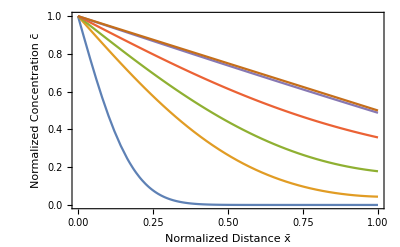

```mathematica
RobinPlot = Plot[{cbarRobin[xBar,0.01],cbarRobin[xBar,0.1],cbarRobin[xBar,0.2],cbarRobin[xBar,0.4],cbarRobin[xBar,1],cbarRobin[xBar,10]},{xBar,0,1},PlotRange->{{0,1},{0,1}},Frame->True, FrameLabel->{"Normalized Distance x̄","Normalized Concentration c̄"}]
```

```mathematica
RobinSignal= -D[cbarRobin[xBar,tBar],xBar];
```

## Compare Neumann, Dirichlet, and Robin

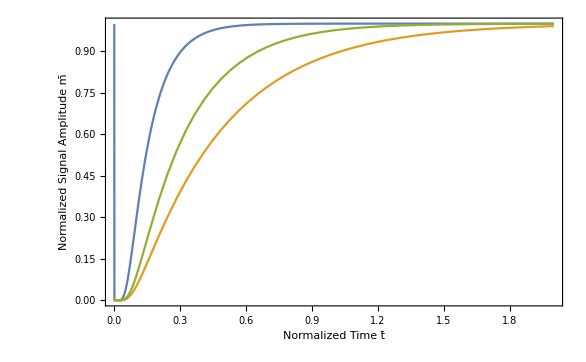

```mathematica
Plot[{sensorDirichlet, sensorNeumann,2RobinSignal/.{xBar->1}}, {tBar,0,2}, PlotRange->{Automatic, {0,1}}, Frame->True, FrameLabel->{"Normalized Time t̄","Normalized Signal Amplitude m̄"}]
```

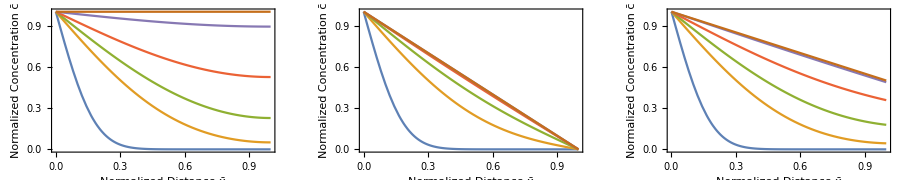

```mathematica
GraphicsRow[{NeumannPlot, DirichletPlot, RobinPlot}]
```